-Graphics3D-

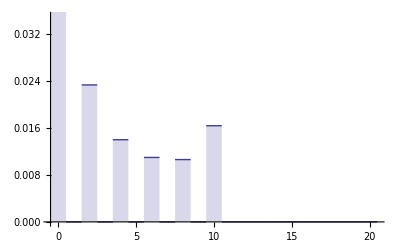

```mathematica
l3 = 5;
max = 20;
DiscretePlot3D[ ThreeJSymbol[{l1,0}, {l2,0}, {l3,0}]^2, {l1,0, max}, {l2,0,max}, ExtentSize->Full, AxesLabel->{Subscript[l, 1],Subscript[l, 2],"Coupling"}]

a = 5;
DiscretePlot[ (ThreeJSymbol[{a,0}, {a+0,0}, {l3b,0}])^2, {l3b,0, max},  ExtentSize->Full ]
```

```mathematica
l1 = 4;
l2 = 4;
l3 = 4;
DiscretePlot3D[(-1)^(m2) *  ThreeJSymbol[{l1,m1}, {l2,-m2}, {l3,m2-m1}], {m1,-l1, l1}, {m2,-l2, l2}, ExtentSize->Full]
```

-Graphics3D-

-Graphics3D-

```mathematica
N[Sum[(-1)^(m2) * ThreeJSymbol[{l1,m1}, {l2,-m2}, {l3,m2-m1}], {m1,-l1, l1}, {m2,-l2, l2}]]
N[Sum[ (-1)^(m1) *ThreeJSymbol[{l1,m1}, {l2,-m1}, {l3,0}], {m1,-l1, l1}]]
```

1.83759

0.

```mathematica
l3=3;
DiscretePlot3D[N[Sum[(-1)^(m2) * ThreeJSymbol[{l1,m1}, {l2,-m2}, {l3,m2-m1}], {m1,-l1, l1}, {m2,-l2, l2}]], {l1,0,2*l3}, {l2, 0, 2*l3},ExtentSize->Full]
```

-Graphics3D-